# Kerr geodesics

## Lagrangian and equations of motion

```mathematica
ClearAll[coords,f,k,g];
coords[λ_]:={t[λ],x[λ],y[λ],z[λ]};

ClearAll[r];
r[x_,y_,z_]:=√(1/2 (-a^2+x^2+y^2+z^2+√(4 a^2 z^2+(-a^2+x^2+y^2+z^2)^2)));

ClearAll[f];
f[x_,y_,z_]:=(2*M*r[x,y,z]^3)/(r[x,y,z]^4+a^2 z^2);

ClearAll[k];
k[x_,y_,z_]:={1,(r[x,y,z]*x+a*y)/(r[x,y,z]^2+a^2),(r[x,y,z]*y-a*x)/(r[x,y,z]^2+a^2),z/r[x,y,z]};

g[x_,y_,z_]:=(DiagonalMatrix[{-1,1,1,1}]+f[x,y,z]*Table[k[x,y,z]⟦μ⟧*k[x,y,z]⟦ν⟧,{μ,1,4},{ν,1,4}]);
ig[x_,y_,z_]:=Inverse[g[x,y,z]];

ClearAll[Lagrangian];
Lagrangian=Collect[1/2*Sum[g[x[λ],y[λ],z[λ]]⟦μ,ν⟧D[coords[λ]⟦μ⟧,λ]D[coords[λ]⟦ν⟧,λ],{μ,1,4},{ν,1,4}],D[coords[λ],λ],Simplify];

ClearAll[tDot,tDotDot,tDerivatives];
tDot=Simplify[Flatten[Solve[En==-D[Lagrangian,t'[λ]],t'[λ]]]];
tDotDot=D[tDot,λ];
tDerivatives=Join[tDot,tDotDot];

ClearAll[EulerLagrangeForx,EulerLagrangeFory,EulerLagrangeForz];
EulerLagrangeForx=((D[D[Lagrangian,x'[λ]],λ]-D[Lagrangian,x[λ]])//.tDerivatives)==0;
EulerLagrangeFory=((D[D[Lagrangian,y'[λ]],λ]-D[Lagrangian,y[λ]])//.tDerivatives)==0;
EulerLagrangeForz=((D[D[Lagrangian,z'[λ]],λ]-D[Lagrangian,z[λ]])//.tDerivatives)==0;
```

## Solution

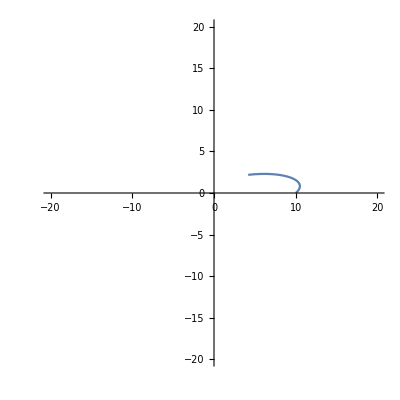

Mass: 1

Particle: Massive

Local positions: {10,0,1/10000000000000000}

Local Veolocities: {0.1,0.1,0.}

```mathematica
ClearAll[M,a,δ];
M=1;
a=M/2;
δ=-1;

ClearAll[x0,y0,z0];
x0=10;
y0=0;
z0=10^-16;

(* Local velocity *)
ClearAll[Vx0,Vy0,Vz0];
Vx0=1/10;
Vy0=1/10;
Vz0=0;

(* Global energy *)
ClearAll[En];
En=1;

ClearAll[λ0,λf];
λ0=0;
λf=40;

ClearAll[wp,ag,pg];
wp=20;
ag=wp-5;
pg=ag;

ClearAll[sol];
sol=Flatten[
NDSolve[
{
EulerLagrangeForx,
EulerLagrangeFory,
EulerLagrangeForz,

(* global = local/lapse *)
x'[λ0]==Vx0/√(-1/ig[x0,y0,z0]⟦1,1⟧),
y'[λ0]==Vy0/√(-1/g[x0,y0,z0]⟦1,1⟧),
z'[λ0]==Vz0/√(-1/g[x0,y0,z0]⟦1,1⟧),

x[λ0]==x0,
y[λ0]==y0,
z[λ0]==z0
},
{x,y,z},
{λ,0,λf},
WorkingPrecision->wp,
AccuracyGoal->ag,
PrecisionGoal->pg,
Method->{"ExplicitRungeKutta","EquationSimplification"->"Solve"}
]
];

ClearAll[range];
range=20;
ParametricPlot[{x[λ]//.sol,y[λ]//.sol},{λ,λ0,λf},PlotRange->{{-range,range},{-range,range}}]


Print["Mass: ",M];
Print["Particle: ",If[δ==0,"Photon","Massive"]]
Print["Local positions: {",x0,",",y0,",",z0,"}"]; 
Print["Local Veolocities: {",Vx0//N,",",Vy0//N,",",Vz0//N,"}"];
```